# 2DEG Magneto-electric Properties

## Floquet Mode Wave Function

```mathematica
Clear All;
```

```mathematica
χ[x_,N_]:= Exp[-x^2/2]/(√(2^N N!√π))HermiteH[N,x];
```

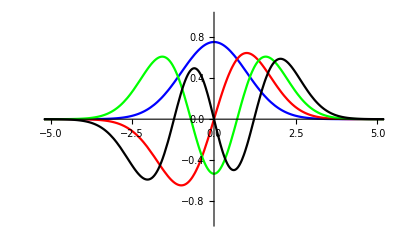

```mathematica
p0= Plot[χ[x,0],{x,-10,10},PlotRange->{{-5,5},{-1,1}},PlotStyle->Blue];
p1= Plot[χ[x,1],{x,-10,10},PlotRange->{{-5,5},{-1,1}},PlotStyle->Red];
p2= Plot[χ[x,2],{x,-10,10},PlotRange->{{-5,5},{-1,1}},PlotStyle->Green];
p3= Plot[χ[x,3],{x,-10,10},PlotRange->{{-5,5},{-1,1}},PlotStyle->Black];
Show[p0,p1,p2,p3]
```

```mathematica
Clear All;
ω = Pi;
Subscript[χ, q][x_,N_,t_]:= Exp[(-(x-Sin[ω*t])^2)/2]/(√(2^N N!√π))HermiteH[N,(x-Sin[ω*t])];
```

Set::write: Tag Times in 0 p is Protected.

Show::gcomb: Could not combine the graphics objects in ….

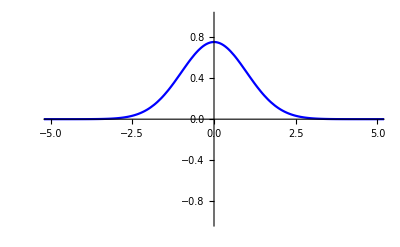
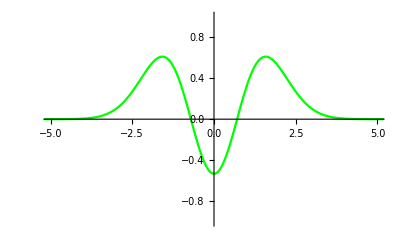
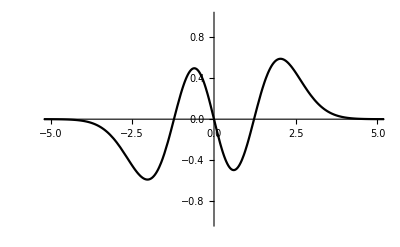
Show[-Graphics-,p01,-Graphics-,-Graphics-]

```mathematica
p00= Plot[Subscript[χ, q][x,0,1],{x,-10,10},PlotRange->{{-5,5},{-1,1}},PlotStyle->Blue];
p01= Plot[Subscript[χ, q][x,1,1],{x,-10,10},PlotRange->{{-5,5},{-1,1}},PlotStyle->Red];
p02= Plot[Subscript[χ, q][x,2,1],{x,-10,10},PlotRange->{{-5,5},{-1,1}},PlotStyle->Green];
p03= Plot[Subscript[χ, q][x,3,1],{x,-10,10},PlotRange->{{-5,5},{-1,1}},PlotStyle->Black];
Show[p00,p01,p02,p03]
```

Set::write: Tag Times in p t is Protected.

Set::write: Tag Times in 2 p t is Protected.

Set::write: Tag Times in 0 p t is Protected.

Set::write: Tag Times in 0 2 p t is Protected.

General::stop: Further output of Set::write will be suppressed during this calculation.

{{Null},{Null^2}}

Show::gcomb: Could not combine the graphics objects in Show[,pt1,pt2,pt00,pt01,pt02].

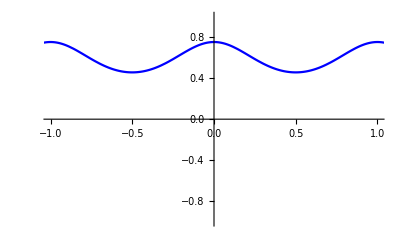
Show[-Graphics-,pt1,pt2,pt00,pt01,pt02]

```mathematica
pt0= Plot[Subscript[χ, q][0,0,t],{t,-10,10},PlotRange->{{-1,1},{-1,1}},PlotStyle->Blue];
pt1= Plot[Subscript[χ, q][0,1,t],{t,-10,10},PlotRange->{{-1,1},{-1,1}},PlotStyle->Red];
{{pt2= Plot[Subscript[χ, q][0,2,t],{t,-10,10},PlotRange->{{-1,1},{-1,1}},PlotStyle->Black];}, {pt01= Plot[Subscript[χ, q][1,0,t],{t,-10,10},PlotRange->{{-1,1},{-1,1}},PlotStyle->Green];
pt02= Plot[Subscript[χ, q][2,0,t],{t,-10,10},PlotRange->{{-1,1},{-1,1}},PlotStyle->Yellow];}}
Show[pt0,pt1,pt2,pt00,pt01,pt02]
```

```mathematica
Φ[x_,y_,t_,N_]:=Re[Subscript[χ, q][x-a,N,t]*Exp[I*b*x]*Exp[I*c*(y-y0)]*Exp[-I*d*Sin[2*ω*t]]];
a=1;
b=1;
c=1;
d=1;
y0=1;
```

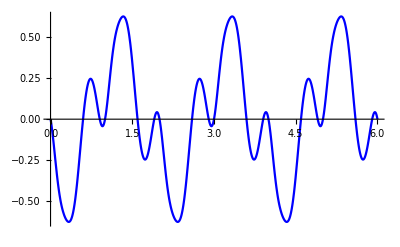

```mathematica
qt0= Plot[Φ[1,1,t,1],{t,0,6},PlotStyle->Blue]
```

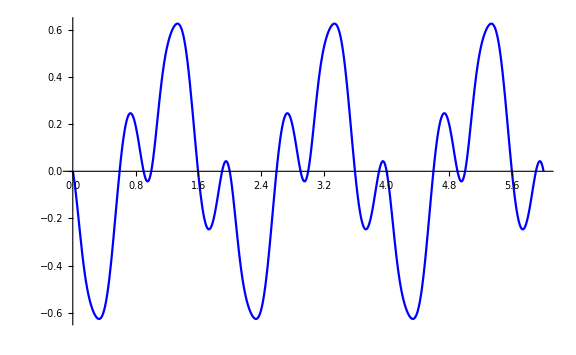

```mathematica
Show[qt0,ImageSize->Large]
```